# Gaussian Kernel basis vs Newtonized Gaussian Kernel basis

## A Somewhat different Perspective

This note is as my dad says “Bass-Ackwards”. It begins with a short example of using the standard basis for collocation, and then discusses two approaches to creating a Newton type basis in the the 2008 and 2011 Schaback papers in which we are simply focusing on the bases.

## Introduction

First, we will look at a simple differential equation taken from Trefethen’s book on spectral methods first using the usual Gaussian kernel basis. Then, following Shaback’s formalism and Fasshauer’s suggestion, we will endeavor to solve this differential equation using the Newtonized version of this basis.

Remark: There is a fair amount of excessive explanation going on and redundant Mathematica as well since neither of you knows this language and I figured you could learn some Mathematica if I took this more pedagogic approach. I am not trying to convert anybody to Mathematica as I have discovered this is an exercise in futility!

## A Simple Collocation Example Using the Gaussian Kernel Basis

The differential equation we will solve is the boundary value problem given by u''(x)=ⅇ^(4x)  u(-1)=u(1)=0. The exact solution can be calculated easily.

```mathematica
sol=u[x]/.DSolve[{u''[x]==Exp[4x],u[-1]==0,u[1]==0},u[x],x][[1]]
```

-(1+ⅇ^8-2 ⅇ^(4+4 x)-x+ⅇ^8 x)/(32 ⅇ^4)

In order to solve this numerically, first we set up our interpolant using n=8 , or, in other words, 7 interior points and 2 boundary points for a total of 9 data points. Note that we separate our boundary points from our interior points in the collocation which is standard. If we include the boundary points we actually get better convergence however. This is not surprising because we are including more information and our system is well behaved on the boundary.

```mathematica
data=Most[Rest[Range[-1,1,1/4]//N]]
```

{-0.75,-0.5,-0.25,0.,0.25,0.5,0.75}

Now we create our interpolant. Note that we need to add two additional degrees of freedom to guarantee that we have can satisfy our boundary condtions.

```mathematica
u[x_,ϵ_]:=Sum[c[j] ⅇ^(-ϵ (x-data[[j]])^2),{j,1,7}]+a+b x
```

Now we construct our second derivative function.

```mathematica
d2u[x_,ϵ_]=D[u[x,ϵ],{x,2}]
```

(-2 ⅇ^(-(0.75+x)^2 ϵ) ϵ+4 ⅇ^(-(0.75+x)^2 ϵ) (0.75+x)^2 ϵ^2) c[1]+(-2 ⅇ^(-(0.5+x)^2 ϵ) ϵ+4 ⅇ^(-(0.5+x)^2 ϵ) (0.5+x)^2 ϵ^2) c[2]+(-2 ⅇ^(-(0.25+x)^2 ϵ) ϵ+4 ⅇ^(-(0.25+x)^2 ϵ) (0.25+x)^2 ϵ^2) c[3]+(-2 ⅇ^(-(0.+x)^2 ϵ) ϵ+4 ⅇ^(-(0.+x)^2 ϵ) (0.+x)^2 ϵ^2) c[4]+(-2 ⅇ^(-(-0.25+x)^2 ϵ) ϵ+4 ⅇ^(-(-0.25+x)^2 ϵ) (-0.25+x)^2 ϵ^2) c[5]+(-2 ⅇ^(-(-0.5+x)^2 ϵ) ϵ+4 ⅇ^(-(-0.5+x)^2 ϵ) (-0.5+x)^2 ϵ^2) c[6]+(-2 ⅇ^(-(-0.75+x)^2 ϵ) ϵ+4 ⅇ^(-(-0.75+x)^2 ϵ) (-0.75+x)^2 ϵ^2) c[7]

Now we create the left hand sides of our interpolation equations.

```mathematica
d2u[#,1]&/@data
```

{-2. c[1]-1.64397 c[2]-0.778801 c[3]+0.142446 c[4]+0.735759 c[5]+0.890848 c[6]+0.737795 c[7],-1.64397 c[1]-2. c[2]-1.64397 c[3]-0.778801 c[4]+0.142446 c[5]+0.735759 c[6]+0.890848 c[7],-0.778801 c[1]-1.64397 c[2]-2. c[3]-1.64397 c[4]-0.778801 c[5]+0.142446 c[6]+0.735759 c[7],0.142446 c[1]-0.778801 c[2]-1.64397 c[3]-2. c[4]-1.64397 c[5]-0.778801 c[6]+0.142446 c[7],0.735759 c[1]+0.142446 c[2]-0.778801 c[3]-1.64397 c[4]-2. c[5]-1.64397 c[6]-0.778801 c[7],0.890848 c[1]+0.735759 c[2]+0.142446 c[3]-0.778801 c[4]-1.64397 c[5]-2. c[6]-1.64397 c[7],0.737795 c[1]+0.890848 c[2]+0.735759 c[3]+0.142446 c[4]-0.778801 c[5]-1.64397 c[6]-2. c[7]}

Now we create the right hand sides of our interpolation equations.

```mathematica
newVals=Rest[Most[Exp[4#]&/@(Range[-1,1,1/4]//N)]]
```

{0.0497871,0.135335,0.367879,1.,2.71828,7.38906,20.0855}

Now we put the lhs and rhs together using Thread. This is a nice function in Mathematica.

```mathematica
Thread[d2u[#,1]&/@data==newVals]
```

{-2. c[1]-1.64397 c[2]-0.778801 c[3]+0.142446 c[4]+0.735759 c[5]+0.890848 c[6]+0.737795 c[7]==0.0497871,-1.64397 c[1]-2. c[2]-1.64397 c[3]-0.778801 c[4]+0.142446 c[5]+0.735759 c[6]+0.890848 c[7]==0.135335,-0.778801 c[1]-1.64397 c[2]-2. c[3]-1.64397 c[4]-0.778801 c[5]+0.142446 c[6]+0.735759 c[7]==0.367879,0.142446 c[1]-0.778801 c[2]-1.64397 c[3]-2. c[4]-1.64397 c[5]-0.778801 c[6]+0.142446 c[7]==1.,0.735759 c[1]+0.142446 c[2]-0.778801 c[3]-1.64397 c[4]-2. c[5]-1.64397 c[6]-0.778801 c[7]==2.71828,0.890848 c[1]+0.735759 c[2]+0.142446 c[3]-0.778801 c[4]-1.64397 c[5]-2. c[6]-1.64397 c[7]==7.38906,0.737795 c[1]+0.890848 c[2]+0.735759 c[3]+0.142446 c[4]-0.778801 c[5]-1.64397 c[6]-2. c[7]==20.0855}

Now we add in our boundary values

```mathematica
Reduce[u[-1,1]==0&&u[1,1]==0&&And@@Thread[d2u[#,1]&/@data==newVals]]
```

c[7]==-637.374&&c[6]==2201.5&&c[5]==-3929.68&&c[4]==4409.19&&c[3]==-3300.32&&c[2]==1550.73&&c[1]==-375.694&&b==11.0163&&a==36.1345

Now we create rules from these solutions

```mathematica
ToRules[Reduce[u[-1,1]==0&&u[1,1]==0&&And@@Thread[d2u[#,1]&/@data==newVals]]]
```

{c[7]→-637.374,c[6]→2201.5,c[5]→-3929.68,c[4]→4409.19,c[3]→-3300.32,c[2]→1550.73,c[1]→-375.694,b→11.0163,a→36.1345}

Now we apply those rules to create our solution

```mathematica
u[x,1]/.ToRules[Reduce[u[-1,1]==0&&u[1,1]==0&&And@@Thread[(d2u[#,1]&/@data)==(Exp[4#]&/@data)]]]
```

36.1345-637.374 ⅇ^(-(-0.75+x)^2)+2201.5 ⅇ^(-(-0.5+x)^2)-3929.68 ⅇ^(-(-0.25+x)^2)+4409.19 ⅇ^(-(0.+x)^2)-3300.32 ⅇ^(-(0.25+x)^2)+1550.73 ⅇ^(-(0.5+x)^2)-375.694 ⅇ^(-(0.75+x)^2)+11.0163 x

All of this can be zipped up into a single function solve. Note that we leave the kernel, and the differential equation as “hard coded”, but it should be easy to create a generic solver from this code.

```mathematica
Clear[solve]
```

```mathematica
solve[n_,ϵ_]:=Module[{data,u,d2u,c,a,b},
data=Most[Rest[Range[-1,1,1/n]//N]];
u[x_,α_]=Sum[c[j] ⅇ^(-α(x-data[[j]])^2),{j,1,2n-1}]+a+b x;
d2u[x_,α_]=D[u[x,α],{x,2}];
u[x,ϵ]/.ToRules[Reduce[u[-1,ϵ]==0&&u[1,ϵ]==0&&And@@Thread[(d2u[#,ϵ]&/@data)==(Exp[4#]&/@data)]]]]
```

Now we test this code.

```mathematica
f=solve[4,1]
```

36.1345-637.374 ⅇ^(-(-0.75+x)^2)+2201.5 ⅇ^(-(-0.5+x)^2)-3929.68 ⅇ^(-(-0.25+x)^2)+4409.19 ⅇ^(-(0.+x)^2)-3300.32 ⅇ^(-(0.25+x)^2)+1550.73 ⅇ^(-(0.5+x)^2)-375.694 ⅇ^(-(0.75+x)^2)+11.0163 x

Good the same answer! We may plot our approximate solution of course.

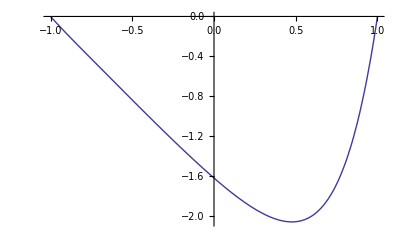

```mathematica
Plot[f,{x,-1,1}]
```

We may plot the approximate solution and the exact solution

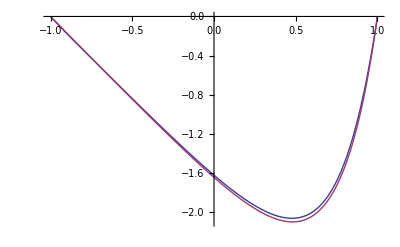

```mathematica
Plot[{f,sol},{x,-1,1}]
```

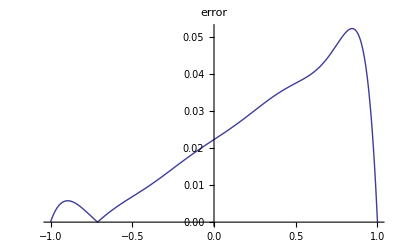

```mathematica
Plot[Abs[f-sol],{x,-1,1},PlotLabel-> "error"]
```

We may include the plotting in a modifed routine of course.

```mathematica
solvePlot[n_,ϵ_]:=Module[{data,u,d2u,c,a,b},
data=Most[Rest[Range[-1,1,1/n]//N]];
u[x_,α_]=Sum[c[j] ⅇ^(-α(x-data[[j]])^2),{j,1,2n-1}]+a+b x;
d2u[x_,α_]=D[u[x,α],{x,2}];
sol=u[x,ϵ]/.ToRules[Reduce[u[-1,ϵ]==0&&u[1,ϵ]==0&&And@@Thread[(d2u[#,ϵ]&/@data)==(Exp[4#]&/@data)]]];
Plot[{sol,-(1+ⅇ^8-2 ⅇ^(4+4 x)-x+ⅇ^8 x)/(32 ⅇ^4)},{x,-1,1}]]
```

Which we may immediately turn into a Manipulate!

```mathematica
Manipulate[solvePlot[n,ϵ],{{n,4},2,20,1},{{ϵ,1},.1,10}]
```

And now we can play around! You will note it is fairly easy to break this, but for small values of n it should work. You will note that as n gets larger you need to localize the kernel more by increasing ϵ or you start to get condition warnings. This is a manifestation of a type of “uncertainty principle” in kernel approximation I think. This notion was developed by Schaback, but I seem to recall he is sort of revising it. We’ll ask Greg about this as I think this is a recent development and perhaps is related to Greg’s HS research which says don’t even bother forming the K matrix!? Finally, you will also note that you can still get nice looking results with bad condition numbers, but eventually this whole process breaks down.

Finally, a big point about how this was programmed. There is both a strength and a weakness to how this was programmed. The strength is that it  was easy! Note that I never formed any matrix myself. I let Reduce detect that it had a linear system on its hands and it passed the problem to LinearSolve which passed it on to other routines like RowReduce so you are still solving a linear system--this has simply been abstracted away in the above code. The big weakness is that we only start to see condition number warnings when things go awry and that’s bad because condition numbers are the main thing we care about. In other words, to make this more useful we would need to figure out the actual matrices being used or some way for Mathematica to spit out condition numbers all the time. This is probably possible I think. Incidentally, this is one reason I told you Palmer that I did not recall encountering any condition number problems on Monday --I had only done this for n=4 and 5 with ϵ=1.

## Newtonized Gaussian Kernel basis (Schaback 2008 Paper)

We attempt to find a fomula for the Newtonized Gaussian Kernel basis. We won’t be successful, because we don’t believe such a basis exists. In fact, we believe that either we don’t understand the process by which a Newton basis is supposed to be created or the definition is an example of incorrect generalization. In fact, this is the reason I did not do this section before, I assumed I was confused

Note we use the notation of the 2008 paper in which the first point is x_0.

### n=0

Since we have one point, this should work. Our goal is to find a formula for c_0.

```mathematica
Clear[v,n,k,K,u]
```

```mathematica
n=0;
```

We are given a set of points X

```mathematica
X=Table[xp[l],{l,0,n}]
```

{xp[0]}

We are given a kernel Kwith which we can form a basis for interpolation

```mathematica
Table[K[x,xp[l]],{l,0,n}]
```

{K[x,xp[0]]}

We wish to find a new basis called the Newton basis

```mathematica
v[x_,k_]:=Sum[c[l]K[x,xp[l]],{l,0,k}]
```

```mathematica
Table[v[x,l],{l,0,n}]//TableForm
```

c[0] K[x,xp[0]]

```mathematica
exp1=Table[v[xp[i],j]==0,{j,1,n},{i,0,j-1}]//Flatten;exp1//TableForm
```

{}

```mathematica
exp2=Table[v[xp[j],j]==1,{j,0,n}];exp2//TableForm
```

c[0] K[xp[0],xp[0]]==1

```mathematica
Union[exp1,exp2]//TableForm
```

c[0] K[xp[0],xp[0]]==1

```mathematica
sol1=Reduce[Union[exp1,exp2],Table[c[j],{j,0,n}]]
```

K[xp[0],xp[0]]≠0&&c[0]==1/K[xp[0],xp[0]]

Now the kernel we are interested in is the Gaussian kernel which is never zero.

```mathematica
sol2=And@@Flatten[Table[K[xp[i],xp[j]]≠ 0,{i,0,n},{j,0,n}]] (*we impose this since we will use Gaussians*)
```

K[xp[0],xp[0]]≠0

```mathematica
Reduce[sol1&&sol2]
```

K[xp[0],xp[0]]≠0&&c[0]==1/K[xp[0],xp[0]]

So we have c_0=1/(K(x_0,x_0))

### n=1

We do the same thing, but now with two points. Our goal is to find a formula for c_1 since we already have c_0.

```mathematica
Clear[v,n,k,K,u]
```

```mathematica
n=1;
```

We are given a set of points X

```mathematica
X=Table[xp[l],{l,0,n}]
```

{xp[0],xp[1]}

We are given a kernel Kwith which we can form a basis for interpolation

```mathematica
Table[K[x,xp[l]],{l,0,n}]
```

{K[x,xp[0]],K[x,xp[1]]}

We wish to find a new basis called the Newton basis

```mathematica
v[x_,k_]:=Sum[c[l]K[x,xp[l]],{l,0,k}]/.{c[0]-> 1/K[xp[0],xp[0]]}
```

```mathematica
Table[v[x,l],{l,0,n}]//TableForm
```

K[x,xp[0]]/K[xp[0],xp[0]]
c[1] K[x,xp[1]]+K[x,xp[0]]/K[xp[0],xp[0]]

```mathematica
exp1=Table[v[xp[i],j]==0,{j,1,n},{i,0,j-1}]//Flatten;exp1//TableForm
```

1+c[1] K[xp[0],xp[1]]==0

```mathematica
exp2=Table[v[xp[j],j]==1,{j,0,n}];exp2//TableForm
```

True
K[xp[1],xp[0]]/K[xp[0],xp[0]]+c[1] K[xp[1],xp[1]]==1

```mathematica
Union[exp1,exp2]//TableForm
```

True
1+c[1] K[xp[0],xp[1]]==0
K[xp[1],xp[0]]/K[xp[0],xp[0]]+c[1] K[xp[1],xp[1]]==1

```mathematica
sol1revised=Reduce[exp1,Table[c[j],{j,0,n}]]
```

K[xp[0],xp[1]]≠0&&c[1]==-1/K[xp[0],xp[1]]

```mathematica
sol1=Reduce[Union[exp1,exp2],Table[c[j],{j,0,n}]]
```

(K[xp[1],xp[0]]==0&&K[xp[0],xp[1]]==-K[xp[1],xp[1]]&&K[xp[1],xp[1]]≠0&&c[1]==1/K[xp[1],xp[1]]&&K[xp[0],xp[0]]≠0)||(K[xp[0],xp[1]]+K[xp[1],xp[1]]≠0&&K[xp[0],xp[0]]==(K[xp[0],xp[1]] K[xp[1],xp[0]])/(K[xp[0],xp[1]]+K[xp[1],xp[1]])&&K[xp[0],xp[1]]≠0&&c[1]==-1/K[xp[0],xp[1]]&&K[xp[1],xp[0]]≠0)

Now the kernel we are interested in is the Gaussian kernel which is never zero.

```mathematica
sol2=And@@Flatten[Table[K[xp[i],xp[j]]≠ 0,{i,0,n},{j,0,n}]] (*we impose this since we will use Gaussians*)
```

K[xp[0],xp[0]]≠0&&K[xp[0],xp[1]]≠0&&K[xp[1],xp[0]]≠0&&K[xp[1],xp[1]]≠0

```mathematica
Reduce[sol1&&sol2]
```

K[xp[0],xp[1]]+K[xp[1],xp[1]]≠0&&K[xp[0],xp[0]]==(K[xp[0],xp[1]] K[xp[1],xp[0]])/(K[xp[0],xp[1]]+K[xp[1],xp[1]])&&K[xp[0],xp[1]]≠0&&c[1]==-1/K[xp[0],xp[1]]&&K[xp[1],xp[0]] K[xp[1],xp[1]]≠0

So we have c_1=-1/(K(x_0,x_1))

### n=2

```mathematica
Clear[v,n,k,K,u]
```

```mathematica
n=2;
```

We are given a set of points X

```mathematica
X=Table[xp[l],{l,0,n}]
```

{xp[0],xp[1],xp[2]}

We are given a kernel Kwith which we can form a basis for interpolation

```mathematica
Table[K[x,xp[l]],{l,0,n}]
```

{K[x,xp[0]],K[x,xp[1]],K[x,xp[2]]}

We wish to find a new basis called the Newton basis

```mathematica
v[x_,k_]:=Sum[c[l]K[x,xp[l]],{l,0,k}]/.{c[0]-> 1/K[xp[0],xp[0]],c[1]-> -1/K[xp[0],xp[1]]}
```

```mathematica
Table[v[x,l],{l,0,n}]//TableForm
```

K[x,xp[0]]/K[xp[0],xp[0]]
K[x,xp[0]]/K[xp[0],xp[0]]-K[x,xp[1]]/K[xp[0],xp[1]]
c[2] K[x,xp[2]]+K[x,xp[0]]/K[xp[0],xp[0]]-K[x,xp[1]]/K[xp[0],xp[1]]

```mathematica
exp1=Table[v[xp[i],j]==0,{j,1,n},{i,0,j-1}]//Flatten;exp1//TableForm
```

True
c[2] K[xp[0],xp[2]]==0
K[xp[1],xp[0]]/K[xp[0],xp[0]]-K[xp[1],xp[1]]/K[xp[0],xp[1]]+c[2] K[xp[1],xp[2]]==0

```mathematica
exp2=Table[v[xp[j],j]==1,{j,0,n}];exp2//TableForm
```

True
K[xp[1],xp[0]]/K[xp[0],xp[0]]-K[xp[1],xp[1]]/K[xp[0],xp[1]]==1
K[xp[2],xp[0]]/K[xp[0],xp[0]]-K[xp[2],xp[1]]/K[xp[0],xp[1]]+c[2] K[xp[2],xp[2]]==1

```mathematica
Union[exp1,exp2]//TableForm
```

True
c[2] K[xp[0],xp[2]]==0
K[xp[1],xp[0]]/K[xp[0],xp[0]]-K[xp[1],xp[1]]/K[xp[0],xp[1]]==1
K[xp[1],xp[0]]/K[xp[0],xp[0]]-K[xp[1],xp[1]]/K[xp[0],xp[1]]+c[2] K[xp[1],xp[2]]==0
K[xp[2],xp[0]]/K[xp[0],xp[0]]-K[xp[2],xp[1]]/K[xp[0],xp[1]]+c[2] K[xp[2],xp[2]]==1

```mathematica
sol1=Reduce[Union[exp1,exp2],Table[c[j],{j,0,n}]];(* a mess *)
```

If the kernel we are interested in is the Gaussian kernel which is positive and therefore never zero then it seems likely that there is no solution.

```mathematica
sol2=And@@Flatten[Table[K[xp[i],xp[j]]≠ 0,{i,0,n},{j,0,n}]] (*we impose this since we will use Gaussians*)
```

K[xp[0],xp[0]]≠0&&K[xp[0],xp[1]]≠0&&K[xp[0],xp[2]]≠0&&K[xp[1],xp[0]]≠0&&K[xp[1],xp[1]]≠0&&K[xp[1],xp[2]]≠0&&K[xp[2],xp[0]]≠0&&K[xp[2],xp[1]]≠0&&K[xp[2],xp[2]]≠0

```mathematica
Reduce[sol1&&sol2]
```

False

As we expected. Actually, you can see what the problem is just by inspection. This system is overdetermined. If we relax requirements and allow for compact support or remove some of the requirements we have imposed then perhaps we can find a solution but I am still skeptical.

## Newtonized Gaussian Kernel basis (Schaback 2011 Paper)

This time we follow the procedure for creating a basis in the 2011 paper. We will first do four iterations of a data set with 10 points so that we can see the process at work. Then we will create a function which does the same thing.

Note we use the notation of the 2008 paper in which the first point is x_1.

### Some practice calculations

We advise rerunning the code in this section carefully. In particular, don’t re-run the definition of X and generate a new set of random points.

```mathematica
Clear[v,n,k,K,Nt,u,x,X]
```

We are given a kernel K.

```mathematica
K[x_,y_]:=ⅇ^(-(x-y)^2)
```

```mathematica
n=10;
```

We are given a set of  n points X

```mathematica
(* X=Sort[RandomReal[{0,1},n]]*)  (* this is how we created the list but we leave it fixed now*)
```

```mathematica
X={0.010751868788584362,0.03334836660416385,0.05614908871468738,0.09820795361143042,0.1933411720333036,0.2561805393968408,0.5155414010088102,0.7366490068724552,0.8370847087665922,0.9607561192208478};
```

We can form the standard basis for interpolation using K

```mathematica
Table[K[x,X[[l]]],{l,1,n}]
```

{ⅇ^(-(-0.0107519+x)^2),ⅇ^(-(-0.0333484+x)^2),ⅇ^(-(-0.0561491+x)^2),ⅇ^(-(-0.098208+x)^2),ⅇ^(-(-0.193341+x)^2),ⅇ^(-(-0.256181+x)^2),ⅇ^(-(-0.515541+x)^2),ⅇ^(-(-0.736649+x)^2),ⅇ^(-(-0.837085+x)^2),ⅇ^(-(-0.960756+x)^2)}

We wish to find a new basis called the Newton basis. With the Gaussian kernel our first Newton basis will be the same as the the first kernel basis.

```mathematica
{Max[Table[K[X[[i]],X[[i]]],{i,1,n}]],First[Position[Table[K[X[[i]],X[[i]]],{i,1,n}],Max[Table[K[X[[i]],X[[i]]],{i,1,n}]]]]}
```

```mathematica
{1.,{1}} (* since they are all the same 1 we take the first one as our max *)
```

```mathematica
Nt[1,x_]:=K[x,X[[1]]]/(√K[X[[1]],X[[1]]])
```

```mathematica
(K[#,#]-∑_(j=1)^1 Nt[j,#]^2)&/@ X//N
```

{0.,0.00102068,0.00411333,0.0151807,0.0645033,0.113497,0.399279,0.651408,0.744786,0.835528}

Note that the maximum now occurs in position 10.

```mathematica
{Max[(K[#,#]-∑_(j=1)^1 Nt[j,#]^2)&/@ X//N],First[Position[(K[#,#]-∑_(j=1)^1 Nt[j,#]^2)&/@ X//N,Max[(K[#,#]-∑_(j=1)^1 Nt[j,#]^2)&/@ X//N]]]}
```

{0.835528,{10}}

We form our u

```mathematica
u[x_]:=K[x,X[[10]]]-∑_(j=1)^1 Nt[j,x]Nt[j,X[[10]]]
```

So we can form our second Newton basis element

```mathematica
Nt[2,x_]:=u[x]/(√(K[X[[10]],X[[10]]]-∑_(j=1)^1 Nt[j,X[[10]]]^2))
```

And we can plot first two elements of the standard basis next to the first two elements of the Newton basis

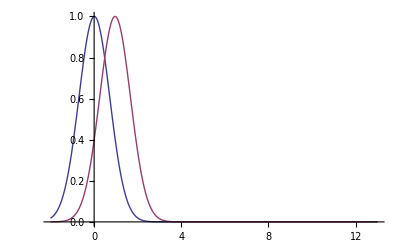
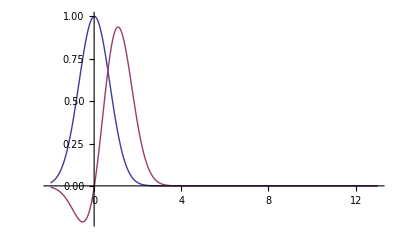

```mathematica
{Plot[{K[x,X[[1]]],K[x,X[[10]]]},{x,-2,13},PlotRange->All],Plot[{Nt[1,x],Nt[2,x]},{x,-2,13},PlotRange->All]}
```

We will now repeat this, with less text and less Mathematica ceremony since we can inspect our list and find the position of the remaining maximal element manually. The reason we did it the first time was so that we could write a program in the next section.

```mathematica
(K[#,#]-∑_(k=1)^2 Nt[k,#]^2)&/@ X//N
```

{0.,0.000642246,0.00252245,0.00884578,0.0328331,0.0519016,0.0930062,0.0454023,0.0167311,0.}

```mathematica
Max[%]
```

0.0930062

```mathematica
u[x_]:=K[x,X[[7]]]-∑_(j=1)^2 Nt[j,x]Nt[j,X[[7]]]
```

```mathematica
Nt[3,x_]:=(K[x,X[[7]]]-∑_(j=1)^2 Nt[j,x]Nt[j,X[[7]]])/(√(K[X[[7]],X[[7]]]-∑_(j=1)^2 Nt[j,X[[7]]]^2))
```

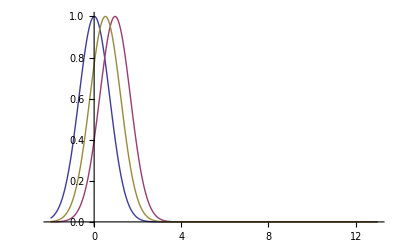
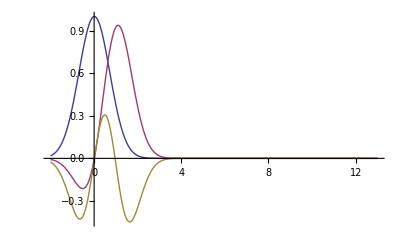

```mathematica
{Plot[{K[x,X[[1]]],K[x,X[[10]]],K[x,X[[7]]]},{x,-2,13},PlotRange->All],Plot[{Nt[1,x],Nt[2,x],Nt[3,x]},{x,-2,13},PlotRange->All]}
```

```mathematica
(K[#,#]-∑_(j=1)^3 Nt[j,#]^2)&/@ X//N
```

{0.,0.0000987671,0.000354161,0.00103537,0.00233555,0.00241696,0.,0.00155347,0.00119509,0.}

```mathematica
Max[%]
```

0.00241696

```mathematica
Nt[4,x_]:=(K[x,X[[6]]]-∑_(j=1)^3 Nt[j,x]Nt[j,X[[6]]])/(√(K[X[[6]],X[[6]]]-∑_(j=1)^3 Nt[j,X[[6]]]^2))
```

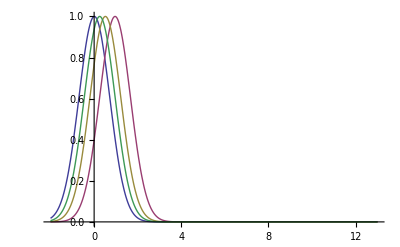
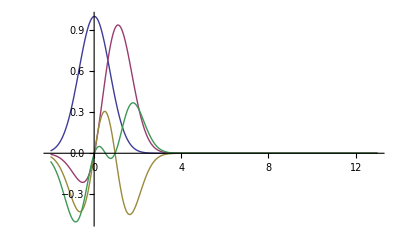

```mathematica
{Plot[{K[x,X[[1]]],K[x,X[[10]]],K[x,X[[7]]],K[x,X[[6]]]},{x,-2,13},PlotRange->All],Plot[{Nt[1,x],Nt[2,x],Nt[3,x],Nt[4,x]},{x,-2,13},PlotRange->All]}
```

### Creating a Program

```mathematica
Clear[v,n,m,k,K,Nt,u,x,X]
```

```mathematica
K[x_,y_]:=ⅇ^(-(x-y)^2)
```

```mathematica
n=4;
```

We are given a set of points X

```mathematica
X=Sort[RandomReal[{0,1},n]]
```

{0.225995,0.272585,0.368313,0.779455}

```mathematica
Clear[Newtonize]
```

```mathematica
Newtonize[X_,K_]:=Module[{Nt,basis,n,m,temp,pos,u},
Nt[1,x_]=K[x,X[[1]]]/(√K[X[[1]],X[[1]]]);
basis={Nt[1,x]};
n=Length[X];
For[m=1,m≤n-1,m++,
temp=N[(K[#,#]-∑_(j=1)^m Nt[j,#]^2)&/@ X];
pos=First[Position[temp,Max[temp]]][[1]];
u[x_]:=K[x,X[[pos]]]-∑_(j=1)^m Nt[j,x]Nt[j,X[[pos]]];
Nt[m+1,x_]=u[x]/(√u[X[[pos]]]);
AppendTo[basis,Nt[m+1,x]]];
basis
]
```

This is probably not a good way to program this in Mathematica since we violate several principles of good Mathematica program design. It is however a transparent translation of the algorithm in the 2011 paper and it should be possible to create a matrix/values based version for use by Matlab programmers.

```mathematica
newtonBasis=Newtonize[X,K]
```

{1. ⅇ^(-(-0.225995+x)^2),1.47751 (ⅇ^(-(-0.779455+x)^2)-0.736153 ⅇ^(-(-0.225995+x)^2)),12.2844 (ⅇ^(-(-0.368313+x)^2)-0.979949 ⅇ^(-(-0.225995+x)^2)-0.268697 (ⅇ^(-(-0.779455+x)^2)-0.736153 ⅇ^(-(-0.225995+x)^2))),393.471 (ⅇ^(-(-0.272585+x)^2)-0.997832 ⅇ^(-(-0.225995+x)^2)-0.0848673 (ⅇ^(-(-0.779455+x)^2)-0.736153 ⅇ^(-(-0.225995+x)^2))-0.393501 (ⅇ^(-(-0.368313+x)^2)-0.979949 ⅇ^(-(-0.225995+x)^2)-0.268697 (ⅇ^(-(-0.779455+x)^2)-0.736153 ⅇ^(-(-0.225995+x)^2))))}

Note that we can expand the newtonBasis so that it looks like a Newton basis. Right now it is in a type of Horner form.

```mathematica
Expand[newtonBasis]//TableForm
```

1. ⅇ^(-(-0.225995+x)^2)
1.47751 ⅇ^(-(-0.779455+x)^2)-1.08767 ⅇ^(-(-0.225995+x)^2)
-3.30077 ⅇ^(-(-0.779455+x)^2)+12.2844 ⅇ^(-(-0.368313+x)^2)-9.60817 ⅇ^(-(-0.225995+x)^2)
8.20995 ⅇ^(-(-0.779455+x)^2)-154.831 ⅇ^(-(-0.368313+x)^2)+393.471 ⅇ^(-(-0.272585+x)^2)-246.935 ⅇ^(-(-0.225995+x)^2)

We may also plot it as before

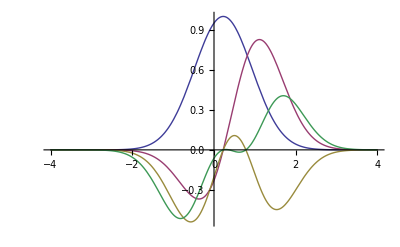

```mathematica
Plot[newtonBasis,{x,-4,4}]
```

By way of contrast, let’s write down and plot the standard basis.

```mathematica
standardBasis=Table[K[x,X[[l]]],{l,1,n}];
```

```mathematica
standardBasis//TableForm
```

ⅇ^(-(-0.225995+x)^2)
ⅇ^(-(-0.272585+x)^2)
ⅇ^(-(-0.368313+x)^2)
ⅇ^(-(-0.779455+x)^2)

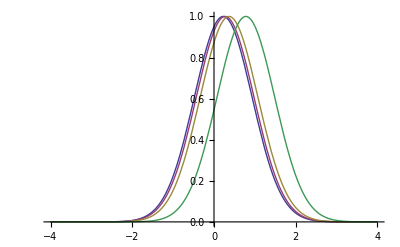

```mathematica
Plot[standardBasis,{x,-4,4}]
```

Naively, it seems intuitive that these basis functions are too close together and therefore will create an ill condtioned interpolation matrix as opposed to the Newton basis where at least the functions look different.

## The Matrices

```mathematica
Clear[v,n,m,k,K,Nt,u,x,X]
```

```mathematica
K[x_,y_]:=ⅇ^(-(x-y)^2)
```

```mathematica
n=4;
```

We are given a set of points X

```mathematica
X=Sort[RandomReal[{0,1},n]]
```

{0.488034,0.588982,0.749127,0.780993}

```mathematica
standardBasis=Table[K[x,X[[l]]],{l,1,n}]
```

{ⅇ^(-(-0.488034+x)^2),ⅇ^(-(-0.588982+x)^2),ⅇ^(-(-0.749127+x)^2),ⅇ^(-(-0.780993+x)^2)}

```mathematica
A=Outer[K[ #1,#2]&,X, X,1];MatrixForm[A]
```

(1. | 0.989861 | 0.934102 | 0.917755
0.989861 | 1. | 0.97468 | 0.963803
0.934102 | 0.97468 | 1. | 0.998985
0.917755 | 0.963803 | 0.998985 | 1.)

As we can see this has a bad condition number. Condition numbers are the last value returned by the LUDecomposition command.

```mathematica
Last[LUDecomposition[A]]
```

3.99212×10^6

On the other hand our Newton basis is

```mathematica
newtonBasis=Newtonize[X,K]
```

{1. ⅇ^(-(-0.488034+x)^2),2.51796 (ⅇ^(-(-0.780993+x)^2)-0.917755 ⅇ^(-(-0.488034+x)^2)),36.5445 (ⅇ^(-(-0.588982+x)^2)-0.989861 ⅇ^(-(-0.488034+x)^2)-0.350946 (ⅇ^(-(-0.780993+x)^2)-0.917755 ⅇ^(-(-0.488034+x)^2))),658.269 (ⅇ^(-(-0.749127+x)^2)-0.934102 ⅇ^(-(-0.488034+x)^2)-0.898448 (ⅇ^(-(-0.780993+x)^2)-0.917755 ⅇ^(-(-0.488034+x)^2))-0.422483 (ⅇ^(-(-0.588982+x)^2)-0.989861 ⅇ^(-(-0.488034+x)^2)-0.350946 (ⅇ^(-(-0.780993+x)^2)-0.917755 ⅇ^(-(-0.488034+x)^2))))}

In expanded form

```mathematica
expandedNewtonBasis=newtonBasis//Expand
```

{1. ⅇ^(-(-0.488034+x)^2),2.51796 ⅇ^(-(-0.780993+x)^2)-2.31087 ⅇ^(-(-0.488034+x)^2),-12.8252 ⅇ^(-(-0.780993+x)^2)+36.5445 ⅇ^(-(-0.588982+x)^2)-24.4037 ⅇ^(-(-0.488034+x)^2),-493.82 ⅇ^(-(-0.780993+x)^2)+658.269 ⅇ^(-(-0.749127+x)^2)-278.107 ⅇ^(-(-0.588982+x)^2)+113.603 ⅇ^(-(-0.488034+x)^2)}

The next thing to do would be to find the condition number of the matrix created by this system. This should not be hard and we expect it is a better number.